```mathematica
(*test*)
```

```mathematica
Clear[a,b]
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\benjamin\Documents\FPII\Moessbauer\code

```mathematica
x={3.01,1.00,0.21,1.95,7.97,0.46,0.66,0.88,1.22,1.43,1.67,1.87,2.16,2.51,3.99,4.98,6.49,9.43,10.92,12.43 };
names={"3.01","1.00","0.21","1.95","7.97","0.46","0.66","0.88","1.22","1.43","1.67","1.87","2.16","2.51","3.99","4.98","6.49","9.43","10.92","12.43"};
```

```mathematica
files=Flatten[Import[StringJoin["../data/background/",#,"mm.TKA"],"CSV"]]&/@names;
```

```mathematica
Dimensions[files]
```

{20,2048}

```mathematica
data=Table[{x[[j]],Sum[files[[j]][[90;;250]][[i]],{i,1,161}]/600.},{j,1,Length[files]}];
```

```mathematica
data
```

{{3.01,27.15},{1.,30.9767},{0.21,40.5283},{1.95,28.14},{7.97,22.9767},{0.46,36.6067},{0.66,33.8917},{0.88,32.3133},{1.22,30.1483},{1.43,29.4067},{1.67,28.8},{1.87,28.285},{2.16,28.285},{2.51,27.7583},{3.99,25.905},{4.98,25.19},{6.49,23.9783},{9.43,21.7483},{10.92,20.3483},{12.43,19.925}}

```mathematica
liplot=ListPlot[data];
```

```mathematica
errordata=Table[{data[[i]],ErrorBar[Sqrt[data[[i]][[2]]/Sqrt[600.]]]},{i,1,Length[data]}];
```

```mathematica
errliplot= ErrorListPlot[errordata];
```

```mathematica
?ErrorListPlot
```

ErrorListPlot[{{y_1,dy_1},{y_2,dy_2},…}] plots points corresponding to a list of values y_1, y_2, …, with corresponding error bars. The errors have magnitudes dy_1,dy_2,….
ErrorListPlot[{{{x_1,y_1},ErrorBar[err_1]},{{x_2,y_2},ErrorBar[err_2]},…}] plots points with specified x and y coordinates and error magnitudes.

```mathematica
model = a Exp[-b v]+c Exp[-d v];
```

```mathematica
nlm= NonlinearModelFit[data, model, {a,b,c,d}, v];
nlm["BestFit"]
```

16.5109 ⅇ^(-1.86792 v)+29.738 ⅇ^(-0.0331478 v)

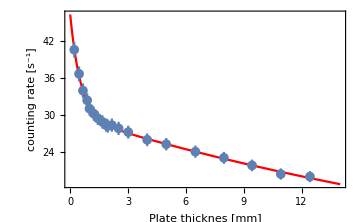

```mathematica
fit=Plot[nlm["BestFit"],{v,0,14}, PlotStyle->Red,ImageSize-> Medium,PlotRange->All,Frame-> True,FrameLabel-> {"Plate thicknes [mm]","counting rate [s^-1]"}];
Show[{fit,errliplot}]
```

```mathematica
nlm["CorrelationMatrix"]//MatrixForm
```

(1. | 0.862715 | 0.111216 | 0.761803
0.862715 | 1. | 0.0425748 | 0.596468
0.111216 | 0.0425748 | 1. | 0.614734
0.761803 | 0.596468 | 0.614734 | 1.)

```mathematica
nlm[0](*Extrapoliere Untergrund*)
```

46.249

```mathematica
nplates={1,1,1,1,2,2,3,4,2,3,2,3,2,1,1,2,2,3,4,4};
yerror=Sqrt[#]/600&/@Table[Sum[files[[j]][[90;;250]][[i]],{i,1,161}],{j,1,Length[files]}];
```

```mathematica
exporttable=Table[Join[data[[i]],{Sqrt[nplates[[i]]]*0.01,yerror[[i]]}],{i,1,Length[files]}]//N;
```

```mathematica
Export["../data/background/data.csv",exporttable,"Table"];
```

```mathematica
test
```